# IBM Rxn API

Will Borrelli

### Function Capabilities

All input requests are lower case.

### Necessary Variable Assignments

```mathematica
(* Initial run of this notebook will prompt you to enter your authorization key. Once you've done that feel free to delete the following cell. *)
```

```mathematica
SystemCredential["authKey"]=InputString["Authorization Key"];
```

```mathematica
authKey=SystemCredential["authKey"];
```

### Input Molecule Images

Inputs of molecules can be direct image inputs:
rxn[“request”, -Graphics-]
or in the form of a variable assigned to have the value of an image:
rxn[“request”, ethenePaintImg1]

```mathematica
ethenePaintImg1=-Graphics-;
```

```mathematica
butadienePaintImg1=-Graphics-;
```

```mathematica
chloroCycHexPaint=-Graphics-;
```

### Function Code

```mathematica
baseURL="rxn.res.ibm.com";
```

```mathematica
rxn[req_String,molecs_List,projID_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
]]
```

```mathematica
(* for getting more outcomes from a prediction that you've already made *)
```

```mathematica
rxn[req_String,projID_String,predID_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
]]
```

```mathematica
(* for making a new retrosynthesis *)
```

```mathematica
rxn[req_String,projID_String,prod_List]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100]},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->"",
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];

retImg
retTable
]]
```

```mathematica
(* for making a new project, listing all project attempts, or recovering a past prediction or retrosynthesis *)
```

```mathematica
rxn[req_String,IDorName_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];
retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];

retImg
retTable
]]
```

```mathematica
(* just for getting all stored projects. if "stored projects" is given as input, outputs a dataset of all stored projects as well as the total number of projects stored *)
```

```mathematica
rxn[req_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,queueState},
Which[(* If[] you want to get all "stored projects", this code block runs *)
req=="stored projects",
myProjects=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

myProjNames=#["name"]&/@myProjects["payload","content"];
myProjIDs=#["id"]&/@myProjects["payload","content"];

nameRule=("Project Name"->#&/@myProjNames);
idRule=("Project ID"->#&/@myProjIDs);

myProjectsData=
Dataset[
Association[#]&/@Transpose[{nameRule,idRule}]]
TableForm[{{ToString[myProjects["payload","totalElements"]]}},TableHeadings->{None,{"Total Stored Projects"}},TableAlignments->Center]
,
req=="queue status",(* get the status of the retrosynthesis queue *)
queueState=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/queue-state"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

queueState
]]
```

### Demo

#### Make a New Project

```mathematica
rxn["new project","myProject"]
```

Project Name | Project ID
myProject | 5ea654986051b700017f0e78

#### Make a New Prediction

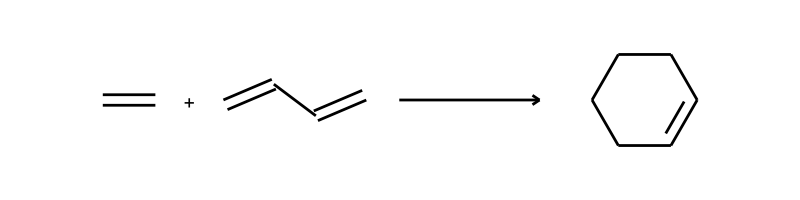
-Graphics- Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3ca26051b70001823dc2 | 0.208485

```mathematica
rxn["new prediction",{-Graphics-,-Graphics-},"5ea654986051b700017f0e78"]
```

```mathematica
rxn["recover prediction","5eaf3ca26051b70001823dc2"]
```

-Graphics- Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3ca26051b70001823dc2 | 0.208485

```mathematica
rxn["new prediction",{"C(=C(C(=C([H])[H])[H])[H])([H])[H]",-Graphics-},"5ea654986051b700017f0e78"]
```

-Graphics- Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.208485

#### Get More Predictions

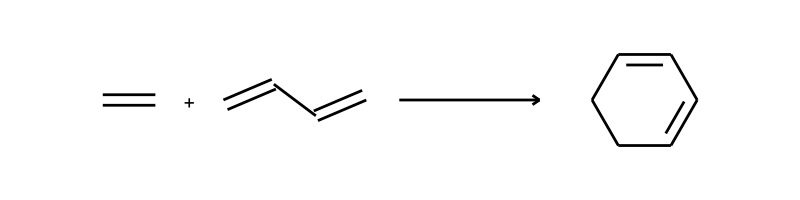
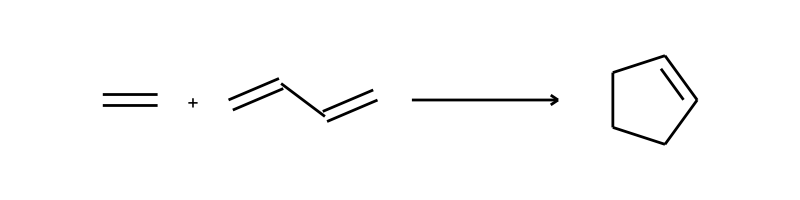
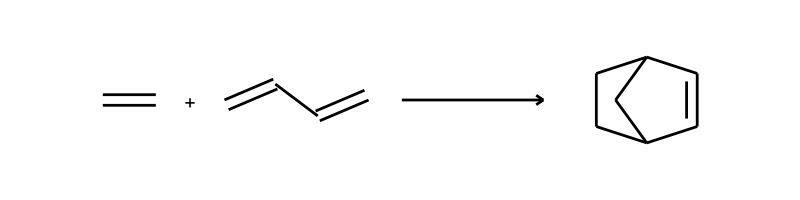
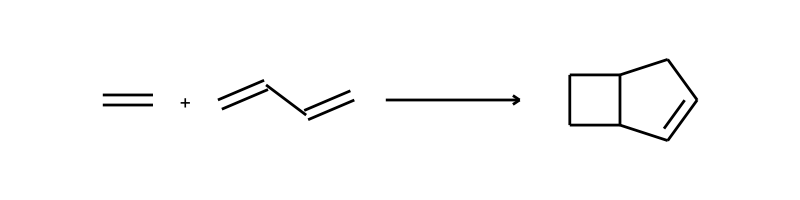
{{-Graphics-,Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.208485},{-Graphics-,Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.12915},{-Graphics-,Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.0519181},{-Graphics-,Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.0465244},{-Graphics-,Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.0400935},{-Graphics-,Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.12915},{-Graphics-,Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.0519181},{-Graphics-,Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.0465244},{-Graphics-,Project Name | Project ID | Prediction ID | Prediction Confidence
myProject | 5ea654986051b700017f0e78 | 5eaf3cc56051b70001823dc5 | 0.0400935}}

```mathematica
rxn["more predictions","5ea654986051b700017f0e78","5eaf3cc56051b70001823dc5"]
```

#### Make a New Retrosynthesis

```mathematica
rxn["new retrosynthesis","5ea654986051b700017f0e78",{-Graphics-}]
```

-Graphics- Project ID | Retrosynthesis ID | Retrosynthesis Confidence | Retrosynthesis Optimization Score | Reaction Class | Sequence Confidence
5ea654986051b700017f0e78 | 5eaf3d816051b70001823dd2 | 0.999 | 1. | Hydroxy to chloro | 0.999

```mathematica
rxn["recover retrosynthesis","5eaf3d816051b70001823dd2"]
```

-Graphics- Project ID | Retrosynthesis ID | Retrosynthesis Confidence | Retrosynthesis Optimization Score | Reaction Class | Sequence Confidence
5ea654986051b700017f0e78 | 5eaf3d816051b70001823dd2 | 0.999 | 1. | Hydroxy to chloro | 0.999

```mathematica
rxn["new retrosynthesis","5ea654986051b700017f0e78",{"ClC1([H])C([H])([H])C([H])([H])C([H])([H])C([H])([H])C1([H])[H]"}]
```

-Graphics- Project ID | Retrosynthesis ID | Retrosynthesis Confidence | Retrosynthesis Optimization Score | Reaction Class | Sequence Confidence
5ea654986051b700017f0e78 | 5eaf3eb86051b70001823e14 | 0.999 | 1. | Hydroxy to chloro | 0.999

#### Queue Status

```mathematica
rxn["queue status"]
```

<|payload→<|itemsInQueue→2,willBeCompletedOn→1588543900000|>,metadata→<|uiMessages→<|errors→{},infos→{},warnings→{}|>,extendedPagination→<||>|>|>

#### Get All Stored Projects

```mathematica
rxn["stored projects"]
```

Total Stored Projects
7